# Scaffold protein titration motif

## The model description

This particular motif describe one phosphorylation-desphosphorylation cycle (can be generalized to any futile cycles) with both kinase (K) and phosphatase (P) can be titrated by a scaffold protein (T).

K + S ⇌ KS → K + S_p
P + S_p ⇌ PS_p → P + S
T + K ⇌ TK
T + P ⇌ TP

The above reactions show a simple system that composed of one scaffold protein, one kinase, one phosphatase and one substrate. Here we try to descibe this simple system with differential equation following the mass action kinetics.

ⅆ[K]/ⅆt=-k[1][K][S]+k[2][KS]+k[3][KS]-k[7][T][K]+k[8][TK],
ⅆ[P]/ⅆt=-k[4][P][S_p]+k[5][PS_p]+k[6][PS_p]-k[9][T][P]+k[10][TP],
ⅆ[S]/ⅆt=-k[1][K][S]+k[2][KS]+k[6][PS_p],
ⅆ[S_p]/ⅆt=-k[4][P][S_p]+k[3][KS]+k[5][PS_p],
ⅆ[KS]/ⅆt=k[1][K][S]-k[2][KS]-k[3][KS],
ⅆ[PS_p]/ⅆt=k[4][P][S_p]-k[5][PS_p]-k[6][PS_p],
ⅆ[T]/ⅆt=-k[7][T][K]+k[8][TK]-k[9][T][P]+k[10][TP],
ⅆ[TK]/ⅆt=k[7][T][K]-k[8][TK],
ⅆ[TP]/ⅆt=k[9][T][P]-k[10][TP].

And the system need to follow these conservation equations:

[K]+[KS]+[TK]=[K_tot],
[P]+[PS_p]+[TP]=[P_tot],
[S]+[S_p]+[KS]+[PS_p]=[S_tot],
[T]+[TK]+[TP]=[T_tot].

In the following setion, we will solve the differential equations to understand the dynamics and behaviour of such system.

## Understanding the dynamics of this simple system at steady states

The reactions are:

K+S⇌KS→K+S_p
P+S_p⇌PS_p→P+S
T+K⇌TK
T+P⇌TP

The species are:

{K(1),P(2),S(3),S_p(4),KS(5),PS_p(6),T(7),TK(8),TP(9)}

Here we have the differential equations:

```mathematica
Clear["Global`*"];
A=Table[0,{10},{9}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];A[[3]][[1]]=1;A[[3]][[4]]=1;A[[3]][[5]]=-1;
A[[4]][[2]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];A[[6]][[2]]=1;A[[6]][[3]]=1;A[[6]][[6]]=-1;
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[8]]=1;A[[8]]=-A[[7]];
A[[9]][[2]]=-1;A[[9]][[7]]=-1;A[[9]][[9]]=1;A[[10]]=-A[[9]];
stoiM=Transpose[A];
ks={k[1]x[1]x[3],k[2]x[5],k[3]x[5],k[4]x[2]x[4],k[5]x[6],k[6]x[6],k[7]x[1]x[7],k[8]x[8],k[9]x[2]x[7],k[10]x[9]};
eqns=stoiM.ks
mC=RowReduce[NullSpace[A]]
```

{-k[1] x[1] x[3]+k[2] x[5]+k[3] x[5]-k[7] x[1] x[7]+k[8] x[8],-k[4] x[2] x[4]+k[5] x[6]+k[6] x[6]-k[9] x[2] x[7]+k[10] x[9],-k[1] x[1] x[3]+k[2] x[5]+k[6] x[6],-k[4] x[2] x[4]+k[3] x[5]+k[5] x[6],k[1] x[1] x[3]-k[2] x[5]-k[3] x[5],k[4] x[2] x[4]-k[5] x[6]-k[6] x[6],-k[7] x[1] x[7]-k[9] x[2] x[7]+k[8] x[8]+k[10] x[9],k[7] x[1] x[7]-k[8] x[8],k[9] x[2] x[7]-k[10] x[9]}

{{1,0,0,0,1,0,0,1,0},{0,1,0,0,0,1,0,0,1},{0,0,1,1,1,1,0,0,0},{0,0,0,0,0,0,1,1,1}}

```mathematica
subsEqns={eqns[[3]],eqns[[5]],eqns[[6]],eqns[[8]],eqns[[9]],x[1]+x[5]+x[8]-Subscript[T, 1],x[2]+x[6]+x[9]-Subscript[T, 2],x[3]+x[4]+x[5]+x[6]-Subscript[T, 3],x[7]+x[8]+x[9]-Subscript[T, 4]}
```

{-k[1] x[1] x[3]+k[2] x[5]+k[6] x[6],k[1] x[1] x[3]-k[2] x[5]-k[3] x[5],k[4] x[2] x[4]-k[5] x[6]-k[6] x[6],k[7] x[1] x[7]-k[8] x[8],k[9] x[2] x[7]-k[10] x[9],-T_1+x[1]+x[5]+x[8],-T_2+x[2]+x[6]+x[9],-T_3+x[3]+x[4]+x[5]+x[6],-T_4+x[7]+x[8]+x[9]}

```mathematica
solution=Solve[{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]],subsEqns[[5]]}==0,{x[3],x[5],x[6],x[8],x[9]}]
```

{{x[3]→((k[2]+k[3]) k[4] k[6] x[2] x[4])/(k[1] k[3] (k[5]+k[6]) x[1]),x[5]→(k[4] k[6] x[2] x[4])/(k[3] (k[5]+k[6])),x[6]→(k[4] x[2] x[4])/(k[5]+k[6]),x[8]→(k[7] x[1] x[7])/k[8],x[9]→(k[9] x[2] x[7])/k[10]}}

Here we substitue the composited parameters:

{(k[2]+k[3])/k[1]→km[1],(k[5]+k[6])/k[4]→km[2],k[6]/k[3]→kcr,k[7]/k[8]→kd[1],k[9]/k[10]→kd[2]}

Then we have:

```mathematica
(* Following the current solution, and substitute the Subscript[T, 1],Subscript[T, 2],Subscript[T, 3],Subscript[T, 4] *)
solution={x[3]->(km[1]*kcr* x[2]* x[4])/(km[2]* x[1]),x[5]->(kcr x[2] x[4])/km[2],x[6]->(x[2] x[4])/km[2],x[8]->kd[1] x[1] x[7],x[9]->kd[2] x[2] x[7]}
```

{x[3]→(kcr km[1] x[2] x[4])/(km[2] x[1]),x[5]→(kcr x[2] x[4])/km[2],x[6]→(x[2] x[4])/km[2],x[8]→kd[1] x[1] x[7],x[9]→kd[2] x[2] x[7]}

```mathematica
t12={T[1]==x[1]+x[5]+x[8],T[2]==x[2]+x[6]+x[9]}/.solution
```

{T[1]==x[1]+(kcr x[2] x[4])/km[2]+kd[1] x[1] x[7],T[2]==x[2]+(x[2] x[4])/km[2]+kd[2] x[2] x[7]}

```mathematica
{t12Sol}=Solve[t12,{x[1],x[2]}]
```

{{x[1]→-(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])/((1+kd[1] x[7]) (km[2]+x[4]+kd[2] km[2] x[7])),x[2]→(km[2] T[2])/(km[2]+x[4]+kd[2] km[2] x[7])}}

```mathematica
t12Sol
```

{x[1]→-(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])/((1+kd[1] x[7]) (km[2]+x[4]+kd[2] km[2] x[7])),x[2]→(km[2] T[2])/(km[2]+x[4]+kd[2] km[2] x[7])}

```mathematica
(x[7]+x[8]+x[9])/.solution
```

x[7]+kd[1] x[1] x[7]+kd[2] x[2] x[7]

```mathematica
x[3]+x[4]+x[5]+x[6]/.solution
```

x[4]+(x[2] x[4])/km[2]+(kcr x[2] x[4])/km[2]+(kcr km[1] x[2] x[4])/(km[2] x[1])

```mathematica
t3={T[3]==x[4]+(x[2] x[4])/km[2]+(kcr x[2] x[4])/km[2]+(kcr km[1] x[2] x[4])/(km[2] x[1])}/.t12Sol
```

{T[3]==x[4]+(T[2] x[4])/(km[2]+x[4]+kd[2] km[2] x[7])+(kcr T[2] x[4])/(km[2]+x[4]+kd[2] km[2] x[7])-(kcr km[1] T[2] x[4] (1+kd[1] x[7]))/(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])}

```mathematica
t32={(km[2]+x[4]+kd[2] km[2] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])*T[3]==(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*x[4]+(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*T[2] x[4]+(-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*kcr T[2] x[4]-(km[2]+x[4]+kd[2] km[2] x[7])*(km[2]+x[4]+kd[2] km[2] x[7])*kcr km[1] T[2] x[4] (1+kd[1] x[7])}
```

```mathematica
t4={T[4]==x[7]+kd[1] x[1] x[7]+kd[2] x[2] x[7]}/.t12Sol
```

{T[4]==x[7]+(kd[2] km[2] T[2] x[7])/(km[2]+x[4]+kd[2] km[2] x[7])-(kd[1] x[7] (-km[2] T[1]-T[1] x[4]+kcr T[2] x[4]-kd[2] km[2] T[1] x[7]))/((1+kd[1] x[7]) (km[2]+x[4]+kd[2] km[2] x[7]))}

```mathematica
t4Sol={Solve[t4,x[7]]}[[1]][[1]]
```

{x[7]→(-kd[1] km[2]-kd[2] km[2]-kd[1] kd[2] km[2] T[1]-kd[1] kd[2] km[2] T[2]+kd[1] kd[2] km[2] T[4]-kd[1] x[4])/(3 kd[1] kd[2] km[2])+(2^(1/3) (-(-kd[1] km[2]-kd[2] km[2]-kd[1] kd[2] km[2] T[1]-kd[1] kd[2] km[2] T[2]+kd[1] kd[2] km[2] T[4]-kd[1] x[4])^2-3 kd[1] kd[2] km[2] (-km[2]-kd[1] km[2] T[1]-kd[2] km[2] T[2]+kd[1] km[2] T[4]+kd[2] km[2] T[4]-x[4]-kd[1] T[1] x[4]+kcr kd[1] T[2] x[4]+kd[1] T[4] x[4])))/(3 kd[1] kd[2] km[2] ((2 kd[1]^3 km[2]^3-3 kd[1]^2 kd[2] km[2]^3-3 kd[1] kd[2]^2 km[2]^3+2 kd[2]^3 km[2]^3-3 kd[1]^3 kd[2] km[2]^3 T[1]-6 kd[1]^2 kd[2]^2 km[2]^3 T[1]+6 kd[1] kd[2]^3 km[2]^3 T[1]-3 kd[1]^3 kd[2]^2 km[2]^3 T[1]^2+6 kd[1]^2 kd[2]^3 km[2]^3 T[1]^2+2 kd[1]^3 kd[2]^3 km[2]^3 T[1]^3+6 kd[1]^3 kd[2] km[2]^3 T[2]-6 kd[1]^2 kd[2]^2 km[2]^3 T[2]-3 kd[1] kd[2]^3 km[2]^3 T[2]+3 kd[1]^3 kd[2]^2 km[2]^3 T[1] T[2]+3 kd[1]^2 kd[2]^3 km[2]^3 T[1] T[2]+6 kd[1]^3 kd[2]^3 km[2]^3 T[1]^2 T[2]+6 kd[1]^3 kd[2]^2 km[2]^3 T[2]^2-3 kd[1]^2 kd[2]^3 km[2]^3 T[2]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[2]^2+2 kd[1]^3 kd[2]^3 km[2]^3 T[2]^3+3 kd[1]^3 kd[2] km[2]^3 T[4]-12 kd[1]^2 kd[2]^2 km[2]^3 T[4]+3 kd[1] kd[2]^3 km[2]^3 T[4]+6 kd[1]^3 kd[2]^2 km[2]^3 T[1] T[4]-3 kd[1]^2 kd[2]^3 km[2]^3 T[1] T[4]-6 kd[1]^3 kd[2]^3 km[2]^3 T[1]^2 T[4]-3 kd[1]^3 kd[2]^2 km[2]^3 T[2] T[4]+6 kd[1]^2 kd[2]^3 km[2]^3 T[2] T[4]-12 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[2] T[4]-6 kd[1]^3 kd[2]^3 km[2]^3 T[2]^2 T[4]-3 kd[1]^3 kd[2]^2 km[2]^3 T[4]^2-3 kd[1]^2 kd[2]^3 km[2]^3 T[4]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[4]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[2] T[4]^2-2 kd[1]^3 kd[2]^3 km[2]^3 T[4]^3+6 kd[1]^3 km[2]^2 x[4]-6 kd[1]^2 kd[2] km[2]^2 x[4]-3 kd[1] kd[2]^2 km[2]^2 x[4]-6 kd[1]^3 kd[2] km[2]^2 T[1] x[4]-6 kd[1]^2 kd[2]^2 km[2]^2 T[1] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[1]^2 x[4]+12 kd[1]^3 kd[2] km[2]^2 T[2] x[4]+9 kcr kd[1]^3 kd[2] km[2]^2 T[2] x[4]-6 kd[1]^2 kd[2]^2 km[2]^2 T[2] x[4]+9 kcr kd[1]^2 kd[2]^2 km[2]^2 T[2] x[4]+3 kd[1]^3 kd[2]^2 km[2]^2 T[1] T[2] x[4]+9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[1] T[2] x[4]+6 kd[1]^3 kd[2]^2 km[2]^2 T[2]^2 x[4]+9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[2]^2 x[4]+6 kd[1]^3 kd[2] km[2]^2 T[4] x[4]-12 kd[1]^2 kd[2]^2 km[2]^2 T[4] x[4]+6 kd[1]^3 kd[2]^2 km[2]^2 T[1] T[4] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[2] T[4] x[4]-9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[2] T[4] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[4]^2 x[4]+6 kd[1]^3 km[2] x[4]^2-3 kd[1]^2 kd[2] km[2] x[4]^2-3 kd[1]^3 kd[2] km[2] T[1] x[4]^2+6 kd[1]^3 kd[2] km[2] T[2] x[4]^2+9 kcr kd[1]^3 kd[2] km[2] T[2] x[4]^2+3 kd[1]^3 kd[2] km[2] T[4] x[4]^2+2 kd[1]^3 x[4]^3+√(((2 kd[1]^3 km[2]^3-3 kd[1]^2 kd[2] km[2]^3-3 kd[1] kd[2]^2 km[2]^3+2 kd[2]^3 km[2]^3-3 kd[1]^3 kd[2] km[2]^3 T[1]-6 kd[1]^2 kd[2]^2 km[2]^3 T[1]+6 kd[1] kd[2]^3 km[2]^3 T[1]-3 kd[1]^3 kd[2]^2 km[2]^3 T[1]^2+6 kd[1]^2 kd[2]^3 km[2]^3 T[1]^2+2 kd[1]^3 kd[2]^3 km[2]^3 T[1]^3+6 kd[1]^3 kd[2] km[2]^3 T[2]-6 kd[1]^2 kd[2]^2 km[2]^3 T[2]-3 kd[1] kd[2]^3 km[2]^3 T[2]+3 kd[1]^3 kd[2]^2 km[2]^3 T[1] T[2]+3 kd[1]^2 kd[2]^3 km[2]^3 T[1] T[2]+6 kd[1]^3 kd[2]^3 km[2]^3 T[1]^2 T[2]+6 kd[1]^3 kd[2]^2 km[2]^3 T[2]^2-3 kd[1]^2 kd[2]^3 km[2]^3 T[2]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[2]^2+2 kd[1]^3 kd[2]^3 km[2]^3 T[2]^3+3 kd[1]^3 kd[2] km[2]^3 T[4]-12 kd[1]^2 kd[2]^2 km[2]^3 T[4]+3 kd[1] kd[2]^3 km[2]^3 T[4]+6 kd[1]^3 kd[2]^2 km[2]^3 T[1] T[4]-3 kd[1]^2 kd[2]^3 km[2]^3 T[1] T[4]-6 kd[1]^3 kd[2]^3 km[2]^3 T[1]^2 T[4]-3 kd[1]^3 kd[2]^2 km[2]^3 T[2] T[4]+6 kd[1]^2 kd[2]^3 km[2]^3 T[2] T[4]-12 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[2] T[4]-6 kd[1]^3 kd[2]^3 km[2]^3 T[2]^2 T[4]-3 kd[1]^3 kd[2]^2 km[2]^3 T[4]^2-3 kd[1]^2 kd[2]^3 km[2]^3 T[4]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[4]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[2] T[4]^2-2 kd[1]^3 kd[2]^3 km[2]^3 T[4]^3+6 kd[1]^3 km[2]^2 x[4]-6 kd[1]^2 kd[2] km[2]^2 x[4]-3 kd[1] kd[2]^2 km[2]^2 x[4]-6 kd[1]^3 kd[2] km[2]^2 T[1] x[4]-6 kd[1]^2 kd[2]^2 km[2]^2 T[1] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[1]^2 x[4]+12 kd[1]^3 kd[2] km[2]^2 T[2] x[4]+9 kcr kd[1]^3 kd[2] km[2]^2 T[2] x[4]-6 kd[1]^2 kd[2]^2 km[2]^2 T[2] x[4]+9 kcr kd[1]^2 kd[2]^2 km[2]^2 T[2] x[4]+3 kd[1]^3 kd[2]^2 km[2]^2 T[1] T[2] x[4]+9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[1] T[2] x[4]+6 kd[1]^3 kd[2]^2 km[2]^2 T[2]^2 x[4]+9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[2]^2 x[4]+6 kd[1]^3 kd[2] km[2]^2 T[4] x[4]-12 kd[1]^2 kd[2]^2 km[2]^2 T[4] x[4]+6 kd[1]^3 kd[2]^2 km[2]^2 T[1] T[4] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[2] T[4] x[4]-9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[2] T[4] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[4]^2 x[4]+6 kd[1]^3 km[2] x[4]^2-3 kd[1]^2 kd[2] km[2] x[4]^2-3 kd[1]^3 kd[2] km[2] T[1] x[4]^2+6 kd[1]^3 kd[2] km[2] T[2] x[4]^2+9 kcr kd[1]^3 kd[2] km[2] T[2] x[4]^2+3 kd[1]^3 kd[2] km[2] T[4] x[4]^2+2 kd[1]^3 x[4]^3))^2+4 (-(-kd[1] km[2]-kd[2] km[2]-kd[1] kd[2] km[2] T[1]-kd[1] kd[2] km[2] T[2]+kd[1] kd[2] km[2] T[4]-kd[1] x[4])^2-3 kd[1] kd[2] km[2] (-km[2]-kd[1] km[2] T[1]-kd[2] km[2] T[2]+kd[1] km[2] T[4]+kd[2] km[2] T[4]-x[4]-kd[1] T[1] x[4]+kcr kd[1] T[2] x[4]+kd[1] T[4] x[4]))^3)))^(1/3))-1/(3 2^(1/3) kd[1] kd[2] km[2])((2 kd[1]^3 km[2]^3-3 kd[1]^2 kd[2] km[2]^3-3 kd[1] kd[2]^2 km[2]^3+2 kd[2]^3 km[2]^3-3 kd[1]^3 kd[2] km[2]^3 T[1]-6 kd[1]^2 kd[2]^2 km[2]^3 T[1]+6 kd[1] kd[2]^3 km[2]^3 T[1]-3 kd[1]^3 kd[2]^2 km[2]^3 T[1]^2+6 kd[1]^2 kd[2]^3 km[2]^3 T[1]^2+2 kd[1]^3 kd[2]^3 km[2]^3 T[1]^3+6 kd[1]^3 kd[2] km[2]^3 T[2]-6 kd[1]^2 kd[2]^2 km[2]^3 T[2]-3 kd[1] kd[2]^3 km[2]^3 T[2]+3 kd[1]^3 kd[2]^2 km[2]^3 T[1] T[2]+3 kd[1]^2 kd[2]^3 km[2]^3 T[1] T[2]+6 kd[1]^3 kd[2]^3 km[2]^3 T[1]^2 T[2]+6 kd[1]^3 kd[2]^2 km[2]^3 T[2]^2-3 kd[1]^2 kd[2]^3 km[2]^3 T[2]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[2]^2+2 kd[1]^3 kd[2]^3 km[2]^3 T[2]^3+3 kd[1]^3 kd[2] km[2]^3 T[4]-12 kd[1]^2 kd[2]^2 km[2]^3 T[4]+3 kd[1] kd[2]^3 km[2]^3 T[4]+6 kd[1]^3 kd[2]^2 km[2]^3 T[1] T[4]-3 kd[1]^2 kd[2]^3 km[2]^3 T[1] T[4]-6 kd[1]^3 kd[2]^3 km[2]^3 T[1]^2 T[4]-3 kd[1]^3 kd[2]^2 km[2]^3 T[2] T[4]+6 kd[1]^2 kd[2]^3 km[2]^3 T[2] T[4]-12 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[2] T[4]-6 kd[1]^3 kd[2]^3 km[2]^3 T[2]^2 T[4]-3 kd[1]^3 kd[2]^2 km[2]^3 T[4]^2-3 kd[1]^2 kd[2]^3 km[2]^3 T[4]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[4]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[2] T[4]^2-2 kd[1]^3 kd[2]^3 km[2]^3 T[4]^3+6 kd[1]^3 km[2]^2 x[4]-6 kd[1]^2 kd[2] km[2]^2 x[4]-3 kd[1] kd[2]^2 km[2]^2 x[4]-6 kd[1]^3 kd[2] km[2]^2 T[1] x[4]-6 kd[1]^2 kd[2]^2 km[2]^2 T[1] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[1]^2 x[4]+12 kd[1]^3 kd[2] km[2]^2 T[2] x[4]+9 kcr kd[1]^3 kd[2] km[2]^2 T[2] x[4]-6 kd[1]^2 kd[2]^2 km[2]^2 T[2] x[4]+9 kcr kd[1]^2 kd[2]^2 km[2]^2 T[2] x[4]+3 kd[1]^3 kd[2]^2 km[2]^2 T[1] T[2] x[4]+9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[1] T[2] x[4]+6 kd[1]^3 kd[2]^2 km[2]^2 T[2]^2 x[4]+9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[2]^2 x[4]+6 kd[1]^3 kd[2] km[2]^2 T[4] x[4]-12 kd[1]^2 kd[2]^2 km[2]^2 T[4] x[4]+6 kd[1]^3 kd[2]^2 km[2]^2 T[1] T[4] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[2] T[4] x[4]-9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[2] T[4] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[4]^2 x[4]+6 kd[1]^3 km[2] x[4]^2-3 kd[1]^2 kd[2] km[2] x[4]^2-3 kd[1]^3 kd[2] km[2] T[1] x[4]^2+6 kd[1]^3 kd[2] km[2] T[2] x[4]^2+9 kcr kd[1]^3 kd[2] km[2] T[2] x[4]^2+3 kd[1]^3 kd[2] km[2] T[4] x[4]^2+2 kd[1]^3 x[4]^3+√(((2 kd[1]^3 km[2]^3-3 kd[1]^2 kd[2] km[2]^3-3 kd[1] kd[2]^2 km[2]^3+2 kd[2]^3 km[2]^3-3 kd[1]^3 kd[2] km[2]^3 T[1]-6 kd[1]^2 kd[2]^2 km[2]^3 T[1]+6 kd[1] kd[2]^3 km[2]^3 T[1]-3 kd[1]^3 kd[2]^2 km[2]^3 T[1]^2+6 kd[1]^2 kd[2]^3 km[2]^3 T[1]^2+2 kd[1]^3 kd[2]^3 km[2]^3 T[1]^3+6 kd[1]^3 kd[2] km[2]^3 T[2]-6 kd[1]^2 kd[2]^2 km[2]^3 T[2]-3 kd[1] kd[2]^3 km[2]^3 T[2]+3 kd[1]^3 kd[2]^2 km[2]^3 T[1] T[2]+3 kd[1]^2 kd[2]^3 km[2]^3 T[1] T[2]+6 kd[1]^3 kd[2]^3 km[2]^3 T[1]^2 T[2]+6 kd[1]^3 kd[2]^2 km[2]^3 T[2]^2-3 kd[1]^2 kd[2]^3 km[2]^3 T[2]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[2]^2+2 kd[1]^3 kd[2]^3 km[2]^3 T[2]^3+3 kd[1]^3 kd[2] km[2]^3 T[4]-12 kd[1]^2 kd[2]^2 km[2]^3 T[4]+3 kd[1] kd[2]^3 km[2]^3 T[4]+6 kd[1]^3 kd[2]^2 km[2]^3 T[1] T[4]-3 kd[1]^2 kd[2]^3 km[2]^3 T[1] T[4]-6 kd[1]^3 kd[2]^3 km[2]^3 T[1]^2 T[4]-3 kd[1]^3 kd[2]^2 km[2]^3 T[2] T[4]+6 kd[1]^2 kd[2]^3 km[2]^3 T[2] T[4]-12 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[2] T[4]-6 kd[1]^3 kd[2]^3 km[2]^3 T[2]^2 T[4]-3 kd[1]^3 kd[2]^2 km[2]^3 T[4]^2-3 kd[1]^2 kd[2]^3 km[2]^3 T[4]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[1] T[4]^2+6 kd[1]^3 kd[2]^3 km[2]^3 T[2] T[4]^2-2 kd[1]^3 kd[2]^3 km[2]^3 T[4]^3+6 kd[1]^3 km[2]^2 x[4]-6 kd[1]^2 kd[2] km[2]^2 x[4]-3 kd[1] kd[2]^2 km[2]^2 x[4]-6 kd[1]^3 kd[2] km[2]^2 T[1] x[4]-6 kd[1]^2 kd[2]^2 km[2]^2 T[1] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[1]^2 x[4]+12 kd[1]^3 kd[2] km[2]^2 T[2] x[4]+9 kcr kd[1]^3 kd[2] km[2]^2 T[2] x[4]-6 kd[1]^2 kd[2]^2 km[2]^2 T[2] x[4]+9 kcr kd[1]^2 kd[2]^2 km[2]^2 T[2] x[4]+3 kd[1]^3 kd[2]^2 km[2]^2 T[1] T[2] x[4]+9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[1] T[2] x[4]+6 kd[1]^3 kd[2]^2 km[2]^2 T[2]^2 x[4]+9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[2]^2 x[4]+6 kd[1]^3 kd[2] km[2]^2 T[4] x[4]-12 kd[1]^2 kd[2]^2 km[2]^2 T[4] x[4]+6 kd[1]^3 kd[2]^2 km[2]^2 T[1] T[4] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[2] T[4] x[4]-9 kcr kd[1]^3 kd[2]^2 km[2]^2 T[2] T[4] x[4]-3 kd[1]^3 kd[2]^2 km[2]^2 T[4]^2 x[4]+6 kd[1]^3 km[2] x[4]^2-3 kd[1]^2 kd[2] km[2] x[4]^2-3 kd[1]^3 kd[2] km[2] T[1] x[4]^2+6 kd[1]^3 kd[2] km[2] T[2] x[4]^2+9 kcr kd[1]^3 kd[2] km[2] T[2] x[4]^2+3 kd[1]^3 kd[2] km[2] T[4] x[4]^2+2 kd[1]^3 x[4]^3))^2+4 (-(-kd[1] km[2]-kd[2] km[2]-kd[1] kd[2] km[2] T[1]-kd[1] kd[2] km[2] T[2]+kd[1] kd[2] km[2] T[4]-kd[1] x[4])^2-3 kd[1] kd[2] km[2] (-km[2]-kd[1] km[2] T[1]-kd[2] km[2] T[2]+kd[1] km[2] T[4]+kd[2] km[2] T[4]-x[4]-kd[1] T[1] x[4]+kcr kd[1] T[2] x[4]+kd[1] T[4] x[4]))^3)))^(1/3)}

```mathematica
t3/.t4Sol
```

{T[3]==x[4]+(T[2] x[4])/(km[2]+x[4]+kd[2] km[2] (1/(3 2 km[2])+1-1/1))+(kcr T[2] x[4])/(km[2]+x[4]+kd[2] km[2] (1))-(kcr km[1] T[2] x[4] (1+kd[1] (1/(3 kd[1] kd[2] km[2])+(2^1 1(11)/(3 4)-(1)^(1/3)/(3 2^(1/3) kd[1] kd[2] km[2]))))/1}
 |  |  |  |

```mathematica
Solve[t3/.t4Sol,x[4]]
```

$Aborted

Here we have the solution for the system we can plug in the values of total concentrations.

```mathematica
(*The following commented region is merely show that there is only one steady state for this system*)
(*jacobian=D[subsEqns,{{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9]}}];
detJ=Collect[Distribute[Det[jacobian]],{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];*)
```

Here we directly solve the system with Mathematica’s Solve function.

```mathematica
Clear["Global`*"];

des={x[1]'[t],x[2]'[t],x[3]'[t],x[4]'[t],x[5]'[t],x[6]'[t],x[7]'[t],x[8]'[t],x[9]'[t]}=={-k[1] x[1][t] x[3][t]+k[2] x[5][t]+k[3] x[5][t]-k[7] x[1][t] x[7][t]+k[8] x[8][t],-k[4] x[2][t] x[4][t]+k[5] x[6][t]+k[6] x[6][t]-k[9] x[2][t] x[7][t]+k[10] x[9][t],-k[1] x[1][t] x[3][t]+k[2] x[5][t]+k[6] x[6][t],-k[4] x[2][t] x[4][t]+k[3] x[5][t]+k[5] x[6][t],k[1] x[1][t] x[3][t]-k[2] x[5][t]-k[3] x[5][t],k[4] x[2][t] x[4][t]-k[5] x[6][t]-k[6] x[6][t],-k[7] x[1][t] x[7][t]-k[9] x[2][t] x[7][t]+k[8] x[8][t]+k[10] x[9][t],k[7] x[1][t] x[7][t]-k[8] x[8][t],k[9] x[2][t] x[7][t]-k[10] x[9][t]};

init={T[1],T[2],T[3],0,0,0,T[4],0,0};

solution=Solve[Table[0,{i,Length[des[[1]]]}]==des[[2]],Table[x[i][t],{i,Length[des[[1]]]}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[3][t]→((k[2]+k[3]) x[5][t])/(k[1] x[1][t]),x[4][t]→(k[3] (k[5]+k[6]) x[5][t])/(k[4] k[6] x[2][t]),x[6][t]→(k[3] x[5][t])/k[6],x[8][t]→(k[7] x[1][t] x[7][t])/k[8],x[9][t]→(k[9] x[2][t] x[7][t])/k[10]},{x[1][t]→0,x[4][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→0,x[9][t]→(k[9] x[2][t] x[7][t])/k[10]},{x[1][t]→0,x[2][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→0,x[9][t]→0},{x[2][t]→0,x[3][t]→0,x[5][t]→0,x[6][t]→0,x[8][t]→(k[7] x[1][t] x[7][t])/k[8],x[9][t]→0}}

Here we substitue the composited parameters:

{(k[2]+k[3])/k[1]→km[1],(k[5]+k[6])/k[4]→km[2],k[3]/k[6]→kcr,k[7]/k[8]→kd[1],k[9]/k[10]→kd[2]}

Then we have:

```mathematica
solution={x[3][t]->(km[1]x[5][t])/(x[1][t]),x[4][t]->(kcr*km[2] x[5][t])/(x[2][t]),x[6][t]->kcr x[5][t],x[8][t]->kd[1] x[1][t] x[7][t],x[9][t]->kd[2] x[2][t] x[7][t]}
```

{x[3][t]→(km[1] x[5][t])/(x[1][t]),x[4][t]→(kcr km[2] x[5][t])/(x[2][t]),x[6][t]→kcr x[5][t],x[8][t]→kd[1] x[1][t] x[7][t],x[9][t]→kd[2] x[2][t] x[7][t]}

## Understanding the dynamics of the simple system with input pertubations (numerical study)

Since, it is a bit difficult to solve the differential equations analytically. Here we try to study them numerically. By defining two different way to characterising the dynamics with scoring their tempral dynamics when presented with input signal perturbation (the changing of [T]). The quantification can be derived from the actually fitness funcitons for ultrasensitive response and adaptive response. Then we save all the parameter sets as well as their score on ultrasensitivity and adaptation.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
AbsoluteTiming[
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t]};


init={totK,totP,totS,0,0,0,totT,0,0};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)

totK=1;totP=1;totS=10;
stepNum=6;
sampleSize=20000;

pars={};
vars=Array[x,9];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
For[num=1,num≤sampleSize,num++,
Block[{k,T,ssthreshold},k[n_]:=k[n]=10^(RandomReal[]*6-3);
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=0.01;

Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step≥stepNum,"StopIntegration"],x[7][t]->x[7][t]+10/(stepNum-1)}]]},vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[stepNum-IntegerPart[stepNum/2]+1]]-x4[[stepNum/2]])]/totS)*Min[((Abs[(x4[[stepNum-IntegerPart[stepNum/2]+1]]-x4[[stepNum/2]])]/Max[Abs[(x4[[IntegerPart[stepNum/2]]]-x4[[1]])],0.001]+Abs[(x4[[stepNum-IntegerPart[stepNum/2]+1]]-x4[[stepNum/2]])]/Max[Abs[(x4[[stepNum]]-x4[[stepNum-IntegerPart[stepNum/2]+1]])],0.001])/2)/10.0,1.0])];
ad=0.0001;
For[i=1,i<stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.5*totS)),1.0]*Min[(0.1)/(Max[Abs[x4[[i+1]]-x4[[i]]],0.001]),1.0])];
];
ad=(ad/0.0001)^(1/(stepNum-1));

ks=Array[k,10];
AppendTo[pars,Join[ks,{us,ad,num,(ks[[2]]+ks[[3]])/ks[[1]],(ks[[5]]+ks[[6]])/ks[[4]],ks[[8]]/ks[[7]],ks[[10]]/ks[[9]]}]];
];
];
];
];
]

(*Plot@@{{{(x[7][t]+x[8][t]+x[9][t]),x[4][t]}/.sol},Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->{"T_tot","S_p"}}
ListPlot[Transpose@{xT,x4},PlotRange->{0,10}]*)
(*Print[pars];*)
transPars=Transpose[pars];
Export["saturationSampling.csv",transPars];
(*Export["unsaturationSampling.csv",transPars];*)
```

{4311.04,Null}

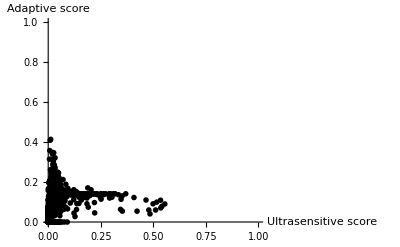

```mathematica
ListPlot[Transpose[{transPars[[11]],transPars[[12]]}],PlotRange->{{0,1},{0,1}},AxesLabel->{"Ultrasensitive score","Adaptive score"},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome"]
```

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
```

```mathematica
maxAndIndex[transPars[[11]]]
```

{0.554555,12278}

```mathematica
maxAndIndex[transPars[[12]]]
```

{0.414253,2962}

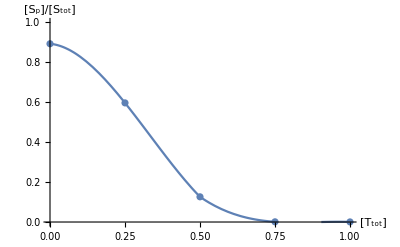

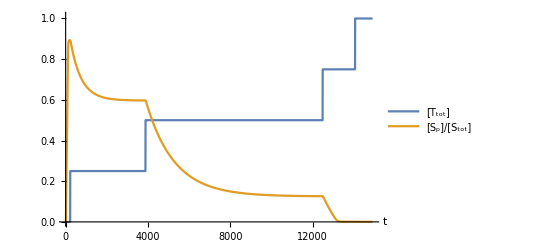

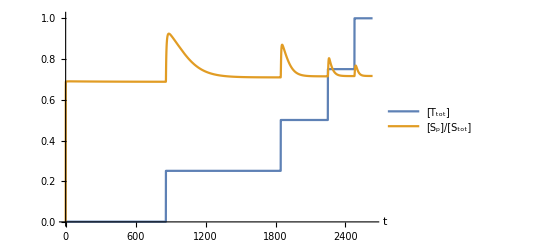

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
usIndex=maxAndIndex[transPars[[11]]]//Last;
adIndex=maxAndIndex[transPars[[12]]]//Last;
stepNum=5;
maxPars=Solve[Array[k,10]==pars[[usIndex]][[Range[10]]]];
Block[{tPer,step,totT},
totT=0.0001;
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]],delta=Through[dvars[t+500]]},WhenEvent[(Norm[df]<ssthreshold&&Norm[delta]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step≥stepNum,"StopIntegration"],x[7][t]->x[7][t]+10/(stepNum-1)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol]/10;
];
Show[Plot[Interpolation[(Transpose@{xT,x4})][x],{x,0,1},PlotRange->{0,1},AxesLabel->{"[T_tot]","[S_p]/[S_tot]"}],ListPlot[Transpose@{xT,x4}]]
Plot@@{{{(x[7][t]+x[8][t]+x[9][t])/10,x[4][t]/totS}/.sol},Flatten@{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[T_tot]","[S_p]/[S_tot]"},{0.85,0.25}],PlotRange->{0,1.01},AxesLabel->{"t"}}

maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];
Block[{tPer,step,totT},
totT=0.01;
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step≥stepNum,"StopIntegration"],x[7][t]->x[7][t]+10/(stepNum-1)}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];
];
Plot@@{{{(x[7][t]+x[8][t]+x[9][t])/10,x[4][t]/totS}/.sol},Flatten@{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[T_tot]","[S_p]/[S_tot]"},{0.85,0.25}],PlotRange->{0,1.01},AxesLabel->{"t"}}
```